```mathematica
(* Method of moments estimator *)
(*Function to generate rate matrix from an edge list and weights*)RateMatrix[edges_List,weights_List,n_Integer]:=Module[{Q},Q=ConstantArray[0,{n,n}];
Do[Q[[edges[[i,1]],edges[[i,2]]]]=weights[[i]],{i,Length[edges]}];
Do[Q[[i,i]]=-Total[Q[[i,All]]],{i,n}];
Q];

(*Function to compute steady-state probabilities*)SteadyStateProbabilities[Q_]:=Module[{n,A,b,π},n=Length[Q];
A=Append[Transpose[Q],ConstantArray[1,n]];
b=Append[ConstantArray[0,n],1];
π=LinearSolve[A,b];
π];

(*Function to compute mean first passage times*)
MeanFirstPassageTimes[Q_]:=Module[{n,Z,T},n=Length[Q];
ss = SteadyStateProbabilities[Q];
Pss = Table[ss, {i,n}];
Z=Inverse[Pss-Q]-Pss;
T=Table[(Z[[j,j]]-Z[[i,j]])/ss[[j]],{i,n},{j,n}];
Simplify[T]];

MeanFirstPassageTimes2[Q_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
T=ConstantArray[0,{n,n}];(*to hold T_{i->j} for i,j=1..n*)
Do[If[i==j,(*If same state,MFPT=0 by definition*)
T[[i,j]]=0,(*Else i!=j,solve the submatrix system:*)
subIdxs=Delete[Range[n],j];(*The set of states except j*)
Qsub=Q[[subIdxs,subIdxs]];(*Q^(j):remove row j,col j*)
rhs=-ConstantArray[1,n-1];(*-1 vector*)(*Solve Qsub x=-1*)
x=LinearSolve[Qsub,rhs];
(*x maps subIdxs->T_{(subIdxs)->j}.We want the entry for i.*)
T[[i,j]]=x[[First@Position[subIdxs,i]]];],{i,1,n},{j,1,n}];
Return[T];];

VarianceFirstPassageTimes[Q_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
m = MeanFirstPassageTimes2[Q];
T=ConstantArray[0,{n,n}];(*to hold T_{i->j} for i,j=1..n*)
Do[If[i==j,(*If same state,MFPT=0 by definition*)
T[[i,j]]=0,(*Else i!=j,solve the submatrix system:*)
subIdxs=Delete[Range[n],j];(*The set of states except j*)
Qsub=Q[[subIdxs,subIdxs]];(*Q^(j):remove row j,col j*)
rhs=-2*m[[subIdxs,j]];(*-1 vector*)(*Solve Qsub x=-2m*)
x=LinearSolve[Qsub,rhs];
(*x maps subIdxs->T_{(subIdxs)->j}.We want the entry for i.*)
T[[i,j]]=x[[First@Position[subIdxs,i]]] - m[[i,j]]^2;],{i,1,n},{j,1,n}];
Return[T];];

LaplaceTransformFPT[Q_,s_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
T=ConstantArray[0,{n,n}];
(*T[[i,j]] will store phi_{i->j}(s)=E[e^{-s T_{i->j}}].*)Do[If[i==j,(*By definition,time from j to j is 0=>Laplace transform=E[e^{-s*0}]=1*)
T[[i,j]]=1,(*i!=j:solve the submatrix system (Q+sI)_{S' x S'}*phi_{S'}=-Q_{S',j},using the boundary condition phi_j(s)=1.*)
subIdxs=Delete[Range[n],j];(*states except j*)
Qsub=Q[[subIdxs,subIdxs]]-s*IdentityMatrix[n-1];
(*Build the inhomogeneous RHS=-Q[i,j],for each i in subIdxs*)rhs=Table[-Q[[subIdxs[[row]],j]],{row,1,n-1}];
x=LinearSolve[Qsub,rhs];
(*x gives phi_{k->j}(s) for k in subIdxs.We want the component corresponding to i.*)T[[i,j]]=x[[First@Position[subIdxs,i]]];],{i,1,n},{j,1,n}];
Return[FullSimplify[T]];];

LaplaceTransformToSetByState[Q_,start_,hit_List,s_]:=Module[{n=Length[Q],subStates,m,results,eqMatrix,eqRHS,hj,sol,iPos},(*If'start' is already in'hit',then the time is 0 with prob=1=>transform=1,but specifically we don't "hit h_j first" if j!=that state.We'll handle it below.*)If[MemberQ[hit,start],(*Then we trivially return a vector of dimension Length[hit],where the entry for'start' is 1,and all others 0.*)
Return[Map[If[#==start,1,0]&,hit]]];
(*Otherwise,we solve one linear system for each h_j in'hit'.*)
subStates=Complement[Range[n],hit];(*non-absorbing set*)m=Length[subStates];
results=Table[((*Build the (Q-sI) submatrix for non-absorbing states.*)eqMatrix=Table[Q[[subStates[[i]],subStates[[j]]]],{i,m},{j,m}];
Do[eqMatrix[[i,i]]-=s,{i,1,m}];
(*RHS=-Q_{i,h_j},for each i in subStates.*)
eqRHS=Table[-Q[[subStates[[i]],hj]],{i,1,m}];
(*Solve and get phi_i^(j)(s).Then extract the'start' component.*)
sol=LinearSolve[eqMatrix,eqRHS];
iPos=First@Position[subStates,start];
sol[[iPos]]),{hj,hit}  (*for each absorbing state in'hit'*)];
Return[results];];
```

```mathematica
(*----------------------------------------------------------------------------------------------------------*)
(*** Loading data ***)

dir = ".julia/dev/LLROpt/mathematica-nbs";
datadir = FileNameJoin[dir,"data"];
plotdir = FileNameJoin[dir,"plots"];
date = "20250322";
fname = "max-F-vs-c-vs-w.wl";
datafile = FileNameJoin[{$HomeDirectory},datadir, date, fname];
results = Get[datafile];
```

```mathematica
(*----------------------------------------------------------------------------------------------------------*)
(*** Plots ***)
```

```mathematica
(*Joint Fisher information rate*)
k = 15;
cvals = Table[10.^x, {x,Subdivide[-1,3,k]}];
wvals = Table[10.^x, {x,Subdivide[-2,2,k]}];
data = Table[Log[results[[i,j]][[1]]],{i,1,k},{j,1,k}];
fig1 = With[{g = GrayLevel[1-#] &},
ListDensityPlot[dataᵀ,
InterpolationOrder->0,(*Controls smoothing:0=none,higher values=smoother interpolation*)
ColorFunction->g,(*Choose a color gradient;alternatives include "TemperatureMap","Rainbow",etc.*)
Frame->True,(*Use a framed plot to enable axis labels*)
FrameLabel->{"log(c_0)","log(ω)"},(*Label your axes*)
LabelStyle->13,
FrameTicks->{
{Table[{i,Round[Log10[wvals[[i]]],0.1]},{i,1,k,3}],Automatic},
{Table[{i,Round[Log10[cvals[[i]]],0.1]},{i,1,k,3}],Automatic}
},
(*ScalingFunctions->{"Log"},*)
PlotLegends->BarLegend[{g, {Min[data],Max[data]}},LegendLabel->Placed["Ḟ",Right],LegendMarkerSize->200],(*Add a colorbar that matches the ColorFunction*)
ImageSize->250
]]
```

-Graphics-

```mathematica
plotfile  = FileNameJoin[plotdir,"max-F-vs-c-w.pdf"];
Export[plotfile,fig1];
```

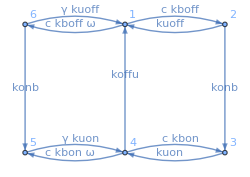

```mathematica
(*Specificity*)

(*Edge lists and weights*)
edges2={{1,2},{2,1},{1,6},{6,1},{4,3},{3,4},{4,5},{5,4},{6,5},{4,1},{2,3}};
weights2={c*kboff,kuoff,ω*c*kboff,γ*kuoff,c*kbon,kuon,ω*c*kbon,γ*kuon,konb,koffu,konb};
nstates2 = 6;
nedges2 = Length[edges2];

(*Plot the circuit*)
edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{5,6},{4,1},{3,2}}}]
```

```mathematica
Q2 = RateMatrix[edges2, weights2, nstates2];
ss2 = SteadyStateProbabilities[Q2];

spec2 = Log[ss2[[3]]/ss2[[5]]];
```

```mathematica
results[[1,1]][[2]]
```

{kboff→0.0888,konb→4.99999,kuon→4.99999,kbon→0.0000625628,koffu→4.99999,kuoff→9.99567×10^-6}

```mathematica
LogSpecificity[c_,ω_,γ_,rates_,edges_]:= Module[{n,Q, weights},
weights = 
Q = RateMatrix[]
]
```

```mathematica
arr = {a,b,c};
```

```mathematica
Thread[{d,e,f}->arr]
```

{2,3,4}

```mathematica
e
```

e